# Rodnost, smrtnost in starostna demografika Slovenije

## Analiza rodnosti, smrtnosti in starostne demografike Slovenije ter njenih sosednjih držav

```mathematica
PodatkiRodnost=Import["C:\\Users\\vidgo\\Documents\\.rom\\projekt\\children-born-per-woman.csv", "Dataset", "HeaderLines"->1]
```

```mathematica
PodatkiZivljenskaDoba=Import["C:\\Users\\vidgo\\Documents\\.rom\\projekt\\life-expectancy.csv", "Dataset", "HeaderLines"->1]
```

```mathematica
PodatkiPovprecnaStarost=Import["C:\\Users\\vidgo\\Documents\\.rom\\projekt\\median-age.csv", "Dataset", "HeaderLines"->1]
```

```mathematica
PodatkiStarostneSkupine=Import["C:\\Users\\vidgo\\Documents\\.rom\\projekt\\population-by-age-group.csv", "Dataset", "HeaderLines"->1]
```

Podatki so iz let 1950-2023. Vse csv datoteke so pridobljene iz ourworldindata.org.

## Rodnost, življenska doba, povprečna starost skozi leta

S pomočjo grafov si bomo ogledali rodnost, pričakovano življensko dobo in povprečno starost v odvisnosti od časa.

### Rodnost

```mathematica
Rodnost[drzava_,barva_]:=ListLinePlot[
Labeled[PodatkiRodnost[Select[#"Entity"==drzava&],4],drzava],
PlotStyle->barva,
ImageSize->Large,
DataRange->{1950,2023}
]
```

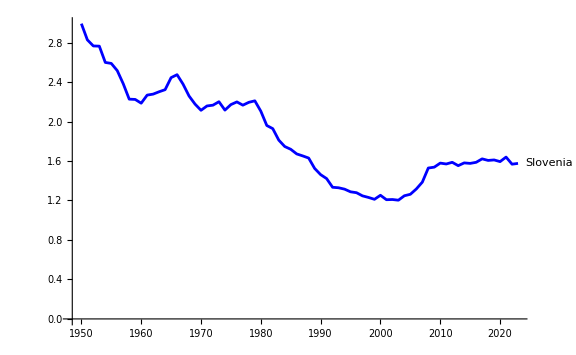

```mathematica
Rodnost["Slovenia", Blue]
```

Rodnost se meri po številu otrok na žensko. Da je populacija stabilna brez migracij, mora to število biti vsaj 2,1. Kot tu vidimo, Slovenija tega ne preseže, vpad rodnosti je pa nekoliko stagniral pri 1,5.

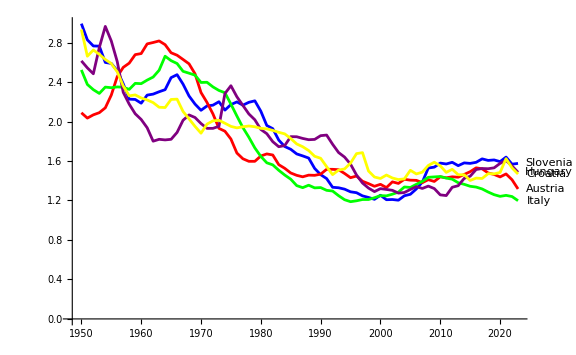

```mathematica
Show[{Rodnost["Slovenia",Blue],Rodnost["Austria",Red],Rodnost["Italy",Green],Rodnost["Hungary",Purple],Rodnost["Croatia", Yellow]}]
```

Podoben trend opazimo tudi pri sosednjih državah. Kot vidimo, ima Italija danes najnižjo rodnost med prikazanimi državami.

### Pričakovana življenska doba

```mathematica
ZivljenskaDoba[drzava_,barva_]:=ListLinePlot[
Labeled[PodatkiZivljenskaDoba[Select[#"Entity"==drzava&],4],drzava],
PlotStyle->barva,
ImageSize->Large,
DataRange->{1950,2023}
]
```

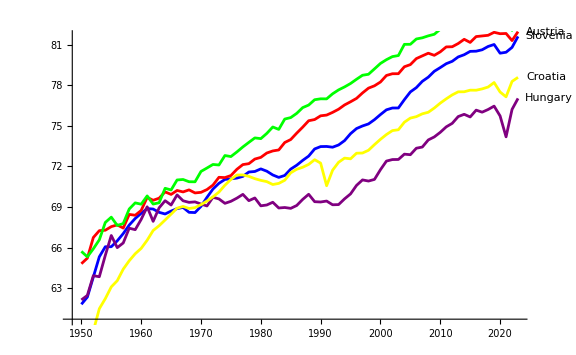

```mathematica
Show[{ZivljenskaDoba["Slovenia",Blue],ZivljenskaDoba["Austria",Red],ZivljenskaDoba["Italy",Green],ZivljenskaDoba["Hungary",Purple],ZivljenskaDoba["Croatia", Yellow]}]
```

Življenska doba zelo konsistentno narašča, s krajšimi vpadi.

### Povprečna starost

```mathematica
PovprenaStarost[drzava_,barva_]:=ListLinePlot[
Labeled[PodatkiPovprecnaStarost[Select[#"Entity"==drzava&],4],drzava],
PlotStyle->barva,
ImageSize->Large,
DataRange->{1950,2023}
]
```

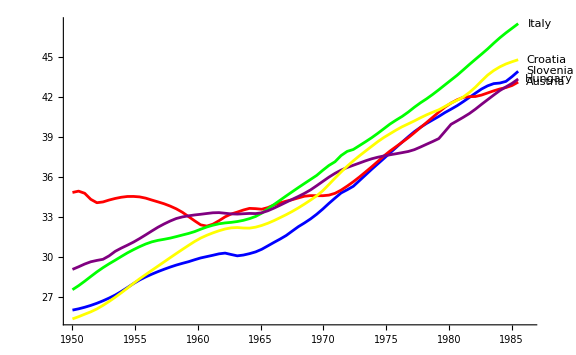

```mathematica
Show[{PovprenaStarost["Slovenia",Blue],PovprenaStarost["Austria",Red],PovprenaStarost["Italy",Green],PovprenaStarost["Hungary",Purple],PovprenaStarost["Croatia", Yellow]},PlotRange->All]
```

Glede na nižanje rodnosti in višanje življenske dobe, ni presenečenje, da povprečna starost prebivalstva povsod v izbranih državah zelo hitro narašča. Opazimo lahko, da ima Italija, ki ima tako najnižjo rodnost kot najvišjo življensko dobo, tudi najvišjo povprečno starost.

## Starostna demografika

Oglejmo si tortni prikaz starostnih skupin glede na državo ter leto.

```mathematica
StarostneSkupine[drzava_,leto_]:=PieChart[
Table[PodatkiStarostneSkupine[Select[#"Entity"==drzava&&#"Year"==leto&],{4,5,6,7,8}]],
ImageSize->Large,
ChartStyle->"Pastel",
ChartLabels->{"65+","25-64","15-24","5-14","0-4"}
]
```

```mathematica
StarostneSkupine["Slovenia",2023]
```

-Graphics-

Prav tako lahko ustvarimo grafični prikaz deleža prebivalstva nad 64 let v odvisnosti od časa.

```mathematica
DelezNad64[drzava_,barva_]:=ListLinePlot[
Labeled[Total[PodatkiStarostneSkupine[Select[#"Entity"==drzava&],4],{2}]/
Total[PodatkiStarostneSkupine[Select[#"Entity"==drzava&],{4,5,6,7,8}],{2}],drzava],
PlotStyle->barva,
ImageSize->Large,
DataRange->{1950,2023}
]
```

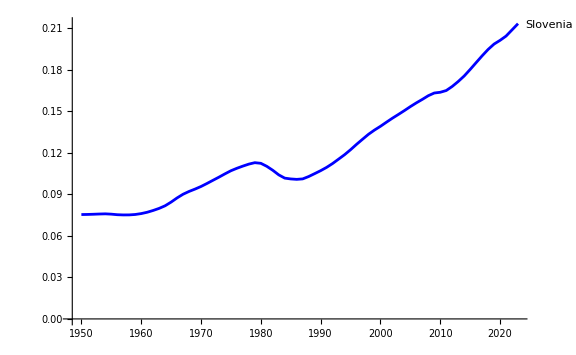

```mathematica
DelezNad64["Slovenia",Blue]
```

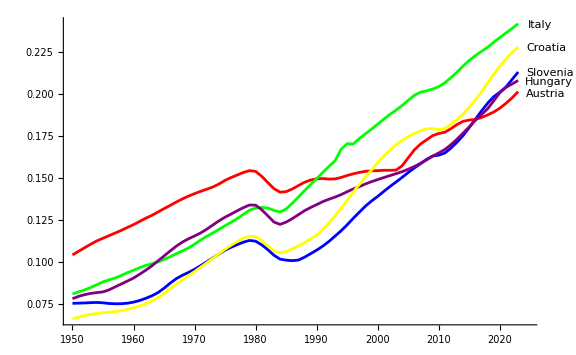

```mathematica
Show[{DelezNad64["Slovenia",Blue],DelezNad64["Austria",Red],DelezNad64["Italy",Green],DelezNad64["Hungary",Purple],DelezNad64["Croatia", Yellow]},PlotRange->All]
```

Ponovno opazimo trend staranja populacije, podobno kot v prejšnjem poglavju.

Funkcijo lahko tudi predelamo tako, da analizira delež poljubne starostne skupine. Uporabnik za spremenljivko skupine vstavi število, ki se nahaja znotraj starostne skupine, ki jo želi prikazati.

```mathematica
StarostnaKategorija[x_]:=Which[x<5,8,5<=x<15,7,15<=x<25,6,25<=x<65,5,x>=65,4]
```

```mathematica
StarostnaKategorijaNiz[x_]:=Which[x<5,"0-4",5<=x<15,"5-14",15<=x<25,"15-24",25<=x<65,"25-64",x>=65,"65+"]
```

```mathematica
DelezSkupine[drzava_,starost_,barva_]:=ListLinePlot[
Labeled[Total[PodatkiStarostneSkupine[Select[#"Entity"==drzava&],StarostnaKategorija[starost]],{2}]/
Total[PodatkiStarostneSkupine[Select[#"Entity"==drzava&],{4,5,6,7,8}],{2}],StarostnaKategorijaNiz[starost]],
PlotStyle->barva,
ImageSize->Large,
DataRange->{1950,2023}
]
```

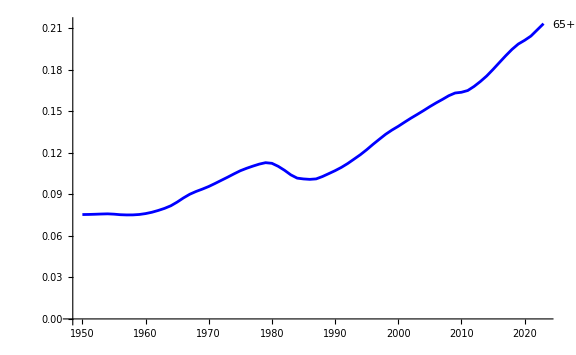

```mathematica
DelezSkupine["Slovenia",70,Blue]
```

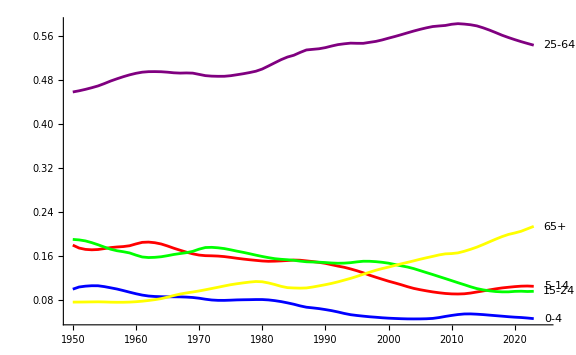

```mathematica
Show[{DelezSkupine["Slovenia",3,Blue],DelezSkupine["Slovenia",10,Red],DelezSkupine["Slovenia",20,Green],DelezSkupine["Slovenia",40,Purple],DelezSkupine["Slovenia",70,Yellow]},PlotRange->All]
```

Iz grafa lahko razberemo, da skozi leta mlajše kategorije padajo, med tem ko je starejših vedno več. Vredno omembe je, da je pričela vpadati tudi skupina 25-64 letnikov.